```mathematica
sps={{Dashing[None],RGBColor[0,0,0]}, {Dashing[Large],RGBColor[1,0,0]},{Dashing[Medium],RGBColor[0,0,1]},{Dashing[Small],RGBColor[0,1,0]},{Dashing[Tiny],RGBColor[0,1,1]}}
```

{{Dashing[None],RGBColor[0, 0, 0]},{Dashing[Large],RGBColor[1, 0, 0]},{Dashing[Medium],RGBColor[0, 0, 1]},{Dashing[Small],RGBColor[0, 1, 0]},{Dashing[Tiny],RGBColor[0, 1, 1]}}

INPUTS

```mathematica
{mass = 939,
radius = 3.}
```

{939,3.}

```mathematica
momenta[energy_]:= (√(energy*energy + 2*mass*energy))/197.327
```

```mathematica
phase[angMomenta_,energy_] := ArcTan[SphericalBesselJ[angMomenta,momenta[energy]*radius]/SphericalBesselY[angMomenta,momenta[energy]*radius]]
```

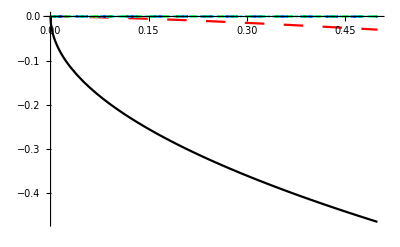

```mathematica
Plot[{phase[0,k],phase[1,k],phase[2,k],phase[3,k],phase[4,k]},{k,0,0.5},PlotStyle->sps]
```

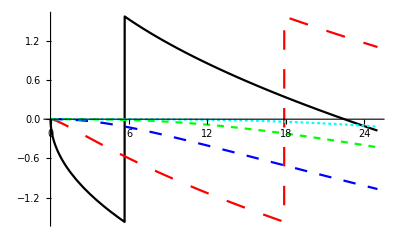

```mathematica
Plot[{phase[0,k],phase[1,k],phase[2,k],phase[3,k],phase[4,k]},{k,0,25},PlotStyle->sps]
```

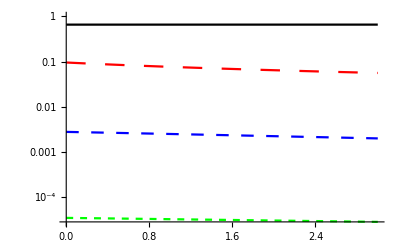

```mathematica
LogPlot[{-phase[0,k]/k^(1/2),-phase[1,k]/k^(3/2),-phase[2,k]/k^(5/2),-phase[3,k]/k^(7/2)},{k,0,3},PlotStyle->sps]
```

```mathematica
sMatrix[angMomenta_,energy_] := Exp[2*I*phase[angMomenta,energy]]
```

```mathematica
crossSection[energy_,lmax_,thetaCos_]:=0.01* Pi/momenta[energy]^2(Abs[Sum[(2 l+1)/(√2)*(sMatrix[l,energy]-1)*LegendreP[l,thetaCos],{l,0,lmax}]])^2
```

```mathematica
ee=0.1;
```

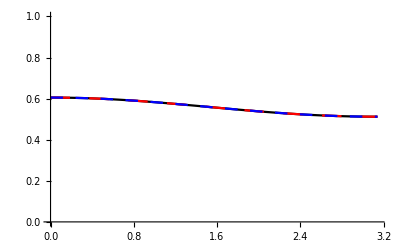

```mathematica
Plot[{crossSection[ee,2,Cos[x]],crossSection[ee,3,Cos[x]],crossSection[ee,4,Cos[x]]},{x,0,Pi},PlotRange->{0,1},PlotStyle->sps]
```

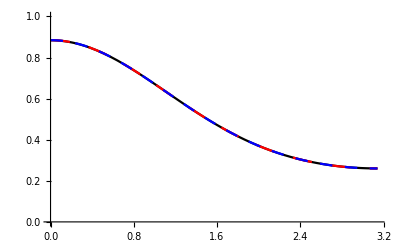

```mathematica
ee=1;Plot[{crossSection[ee,2,Cos[x]],crossSection[ee,3,Cos[x]],crossSection[ee,4,Cos[x]]},{x,0,Pi},PlotRange->{0,1},PlotStyle->sps]
```

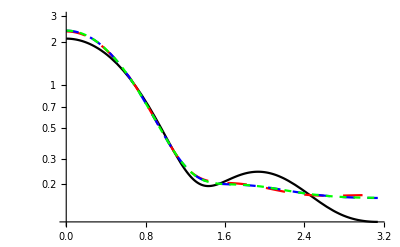

```mathematica
ee=10;LogPlot[{crossSection[ee,2,Cos[x]],crossSection[ee,3,Cos[x]],crossSection[ee,4,Cos[x]],crossSection[ee,5,Cos[x]]},{x,0,Pi},PlotRange->{0,3},PlotStyle->sps]
```

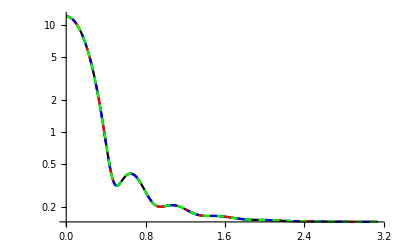

```mathematica
ee=100;LogPlot[{crossSection[ee,10,Cos[x]],crossSection[ee,15,Cos[x]],crossSection[ee,20,Cos[x]],crossSection[ee,25,Cos[x]]},{x,0,Pi},PlotRange->All,PlotStyle->sps]
```

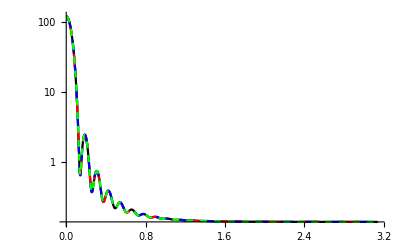

```mathematica
ee=1000;LogPlot[{crossSection[ee,50,Cos[x]],crossSection[ee,60,Cos[x]],crossSection[ee,70,Cos[x]],crossSection[ee,80,Cos[x]]},{x,0,Pi},PlotRange->All,PlotStyle->sps]
```

```mathematica
csPartial[energy_,lPart_,thetaCos_]:=0.01* Pi/momenta[energy]^2(Abs[(2 *lPart+1)/(√2)*(sMatrix[lPart,energy]-1)*LegendreP[lPart,thetaCos]])^2
```

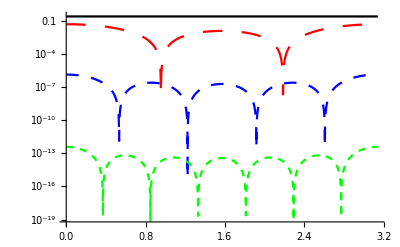

```mathematica
ee=5;LogPlot[{csPartial[ee,0,Cos[x]],csPartial[ee,2,Cos[x]],csPartial[ee,4,Cos[x]],csPartial[ee,6,Cos[x]]},{x,0,Pi},PlotRange->All,PlotStyle->sps]
```

```mathematica
totalCS[energy_,lmax_]:=0.01*Pi/momenta[energy]^2 Sum[(2l+1)Sin[phase[l,energy]]^2,{l,0,lmax}]
```

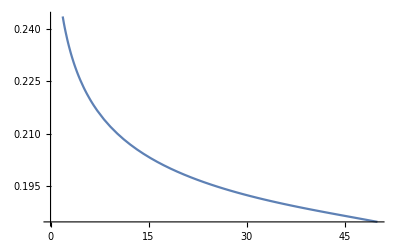

```mathematica
Plot[totalCS[e,5],{e,0,50}]
```